```mathematica
ResourceFunction["DarkMode"][]
```

```mathematica
mic = SampledEntityClass["", 10]
```

SampledEntityClass[Company,10]

```mathematica
mi
```

```mathematica
mic["Dataset"]
```

Missing[UnknownEntity,{Company,Microsoft}]

```mathematica
coms = EntityList[SampledEntityClass["Company",2]]
```

{01 Communique Laboratory,01Cyberaton}

```mathematica
Entity["Company","ChipotleMexicanGrill::2dm57"]["Properties"]
```

{accounts payable,accounts receivable,accumulated depreciation,additional paid in capital,address,amortization,assets turnover,beginning cash position,capital expenditures,cash,cash and cash equivalents,cash dividends paid,cash equivalents,cash flow from continuing financing activities,cash flow from continuing investing activities,cash flow from continuing operating activities,cash flow from discontinued operation,cash from discontinued financing activities,cash from discontinued investing activities,change in accrued expense,change in interest payable,change in inventory,change in payable,change in tax payable,change in working capital,change in cash and cash equivalents,change in receivables,city,common shares,common stock,common stock issuance,common stock payments,coordinates,corporate structure,cost of revenue,current accrued expenses,current assets,current debt,current liabilities,current notes payable,current ratio,deferred assets,deferred costs,deferred tax assets,defunct date,depreciation,depreciation amortization depletion,depreciation and amortization,earnings before interest and tax,earnings before interest tax depreciation and amortization,total employees,end cash position,entity classes,entity type list,equity investments,financial health grade,financial leverage,financing cash flow,former names,founding date,free cash flow,general and administrative expense,goodwill,goodwill and other intangible assets,gross loan,gross margin,gross properties plants and equipment,gross profit,growth grade,held to maturity securities,company logo,income tax payable,sector,interest bearing deposits assets,interest bearing deposits liabilities,interest expense,interest expense from non-operating activities,interest expense from operating activities,interest income,interest income from non-operating activities,interest income from operating activities,interest payable,inventory,inventory turnover,investing cash flow,long-term debt,long-term debt issuance,long-term debt payments,debt to capital ratio,long-term investments,metropolitan area,minority interest,money market investments,name,net business purchase and sale,net income,net income earned by common stockholders,net income from continuous operations,net income from discontinuous operations,net income from extraordinary,net income growth,net intangibles purchase and sale,net interest income,net investment income,net investment purchase and sale,net loan,net margin,net non-operating interest income and expense,net operating interest income and expense,fixed assets,net purchase and sale of properties plants and equipments,net technology purchase and sale,non-current accrued expenses,non-current notes receivables,non-interest expense,non-interest income,notes receivable,operating cash flow,operating expense,operating income,operating income growth,operating margin,operating revenue,other financial instruments,other income expense,other intangible assets,other short-term investments,ownership type,position,postal code,predecessor companies,preferred stock,preferred stock dividends,preferred stock issuance,preferred stock payments,pre-tax income,profitability grade,purchase of business,purchase of equity securities,purchase of fixed maturity securities,purchase of intangibles,purchase of investment,purchase of long-term investments,purchase of properties plants and equipments,purchase of short-term investments,purchase of technology,research and development,retained earnings,revenue growth,revenue per employee,return on assets,return on equity,sales of business,sale of intangibles,sales of investment,sale of long-term investments,sales of properties plants and equipments,sales of short-term investments,sales of equity securities,sales of fixed maturity securities,selling and marking expense,selling general and administration,short-term debt issuance,short-term debt payments,status,stockholders equity,successor companies,tax provision,total assets,total debt,total deposits,total expenses,total investments,total liabilities,total non-current assets,total non-current liabilities,total revenue,total tax payable,trading liabilities,trading securities,treasury stock,unearned income,website,working capital}

```mathematica
EntityProperty["Company","GrossProfit"]
```

gross profit

EntityProperty[Company, GrossProfit]

```mathematica
Keys[topCompaniesByProfit][[1]]["Employees"]
```

1500000 people

```mathematica
nEmployees = Map[#["Employees"]&, Keys[topCompaniesByProfit]]
```

{1500000 people,161000 people,182381 people,2100000 people,221000 people,62000 people,163423 people,66185 people,468000 people,111683 people,93000 people,186000 people,101279 people,117100 people,43846 people,67600 people,536000 people,383000 people,300000 people,160700 people,66279 people,21936 people,207930 people,328000 people,152700 people,417173 people,334600 people,32188 people,674907 people,96000 people,207000 people,157953 people,148861 people,333840 people,471600 people,45149 people,81000 people,590386 people,375235 people,315000 people,71000 people,224955 people,100920 people,91573 people,101703 people,276000 people,69000 people,107000 people,83000 people,77300 people}

```mathematica
B
```

```mathematica
topCompaniesByEmployees = EntityValue[
 EntityClass[
  "Company", {EntityProperty["Company", "Employees"] -> 
    TakeLargest[50]}], 
 EntityProperty["Company", "Employees"], "EntityAssociation"]
```

```mathematica
Entity["Company","WalMartStores::zsp93"]["Dataset"]
```

```mathematica
Entity["Artwork","GirlWithAPearlEarring::JohannesVermeer"]["CompletionDate"]
```

Year: 1665

```mathematica
DateObject[{1600}]
```

Year: 1600

```mathematica
oldArtClass = EntityClass["Artwork", 
{"CompletionDate" -> 
   Between[{DateObject[{1600}], DateObject[{1650}]}]}]
```

EntityClass[Artwork,{CompletionDate→Between[{Year: 1600,Year: 1650}]}]

```mathematica
art1100s = EntityList[oldArtClass];
```

```mathematica
Length[art1100s]
```

191

```mathematica
imgs = #["Image"]&/@ art1100s[[31;;60]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Missing[NotAvailable],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Missing[NotAvailable]}

```mathematica
topCompaniesByProfit = EntityValue[
 EntityClass[
  "Company", {EntityProperty["Company", "GrossProfit"] -> 
    TakeLargest[50]}], 
 EntityProperty["Company", "GrossProfit"], "EntityAssociation"]
```

<|Amazon.com→256202000000 $,Apple→169148000000 $,Alphabet→166756000000 $,Walmart→155045000000 $,Microsoft→151597000000 $,Exxon Mobil→111378000000 $,Electricite de France→1.09495×10^11 $,Meta Platforms→100246000000 $,Gazprom→9.47703×10^10 $,Samsung Electronics Co→9.01392×10^10 $,Shell→89910000000 $,Comcast→84560000000 $,TotalEnergies→80844000000 $,Verizon Communications→78628000000 $,Chevron→77110000000 $,BP→76944000000 $,United Parcel Service→73681000000 $,Berkshire Hathaway→72807000000 $,CVS Health→72673000000 $,AT&T→71966000000 $,Enel→6.5133×10^10 $,Equinor→64621000000 $,Deutsche Telekom→6.36564×10^10 $,FedEx→62347000000 $,Johnson & Johnson→60230000000 $,PetroChina Co→5.97105×10^10 $,Rosneft Oil→5.74463×10^10 $,Eni→5.51981×10^10 $,Volkswagen→5.36274×10^10 $,Lukoil→5.34459×10^10 $,HCA Healthcare→53415000000 $,LVMH→5.31476×10^10 $,Christian Dior→5.31465×10^10 $,Nippon Telegraph→5.19451×10^10 $,Home Depot→51378000000 $,Petrobras Brasileiro→5.12685×10^10 $,Morgan Stanley→50534000000 $,Deutsche Post→5.04462×10^10 $,Toyota Motor→5.0061×10^10 $,PepsiCo→49634000000 $,T-Mobile US→48734000000 $,Alibaba Group Holding→4.74208×10^10 $,Roche Holding→4.63012×10^10 $,Sanofi→4.45515×10^10 $,Novartis→44394000000 $,Nestle→4.38781×10^10 $,Merck & Co→43351000000 $,Procter & Gamble→40850000000 $,Pfizer→40658000000 $,American Express→39861000000 $|>

```mathematica
#[EntityProperty["Company", "Employees"]]&/@ topCompaniesByProfit
```

<|Amazon.com→(256202000000 $)[total employees],Apple→(169148000000 $)[total employees],Alphabet→(166756000000 $)[total employees],Walmart→(155045000000 $)[total employees],Microsoft→(151597000000 $)[total employees],Exxon Mobil→(111378000000 $)[total employees],Electricite de France→(1.09495×10^11 $)[total employees],Meta Platforms→(100246000000 $)[total employees],Gazprom→(9.47703×10^10 $)[total employees],Samsung Electronics Co→(9.01392×10^10 $)[total employees],Shell→(89910000000 $)[total employees],Comcast→(84560000000 $)[total employees],TotalEnergies→(80844000000 $)[total employees],Verizon Communications→(78628000000 $)[total employees],Chevron→(77110000000 $)[total employees],BP→(76944000000 $)[total employees],United Parcel Service→(73681000000 $)[total employees],Berkshire Hathaway→(72807000000 $)[total employees],CVS Health→(72673000000 $)[total employees],AT&T→(71966000000 $)[total employees],Enel→(6.5133×10^10 $)[total employees],Equinor→(64621000000 $)[total employees],Deutsche Telekom→(6.36564×10^10 $)[total employees],FedEx→(62347000000 $)[total employees],Johnson & Johnson→(60230000000 $)[total employees],PetroChina Co→(5.97105×10^10 $)[total employees],Rosneft Oil→(5.74463×10^10 $)[total employees],Eni→(5.51981×10^10 $)[total employees],Volkswagen→(5.36274×10^10 $)[total employees],Lukoil→(5.34459×10^10 $)[total employees],HCA Healthcare→(53415000000 $)[total employees],LVMH→(5.31476×10^10 $)[total employees],Christian Dior→(5.31465×10^10 $)[total employees],Nippon Telegraph→(5.19451×10^10 $)[total employees],Home Depot→(51378000000 $)[total employees],Petrobras Brasileiro→(5.12685×10^10 $)[total employees],Morgan Stanley→(50534000000 $)[total employees],Deutsche Post→(5.04462×10^10 $)[total employees],Toyota Motor→(5.0061×10^10 $)[total employees],PepsiCo→(49634000000 $)[total employees],T-Mobile US→(48734000000 $)[total employees],Alibaba Group Holding→(4.74208×10^10 $)[total employees],Roche Holding→(4.63012×10^10 $)[total employees],Sanofi→(4.45515×10^10 $)[total employees],Novartis→(44394000000 $)[total employees],Nestle→(4.38781×10^10 $)[total employees],Merck & Co→(43351000000 $)[total employees],Procter & Gamble→(40850000000 $)[total employees],Pfizer→(40658000000 $)[total employees],American Express→(39861000000 $)[total employees]|>

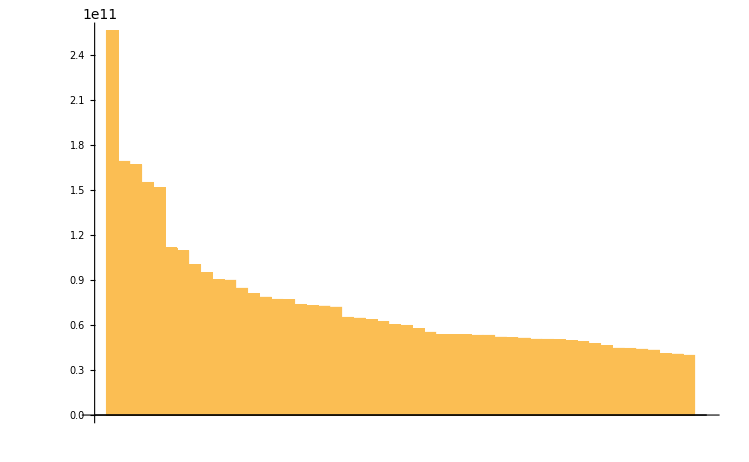

```mathematica
BarChart[KeyValueMap[Tooltip[#2, #1["Name"]]&, topCompaniesByProfit]]
```

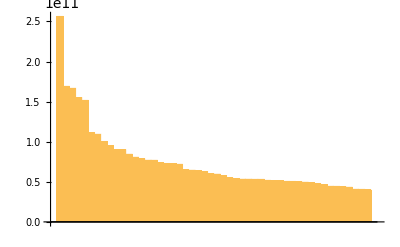

```mathematica
BarChart[topCompaniesByProfit]
```